#### Elementos de la representación matricial del Hamiltoniano LMG en la base |j,m) con ϵ =1, ℏ=1 y γy = 3γx

```mathematica
Hel[j_,m_,k_]:= m KroneckerDelta[m,k]-1/2(γx/(2j-1))(√(j(j+1)-m(m+1))√(j(j+1)-(m+1)(m+2))KroneckerDelta[m+2,k]+√(j(j+1)-m(m-1))√(j(j+1)-(m-1)(m-2))KroneckerDelta[m-2,k]-4(j(j+1)-m^2)KroneckerDelta[m,k])
```

Paridad positiva  | j, m) -j a j en pasos de 2

```mathematica
j=100;
γx=-(2j-1)/((2j-172)Sqrt[3] );
```

```mathematica
Hmtrx= Table[Table[Hel[j,m,k],{m,-j,j,2}],{k,-j,j,2}];
```

El cruce evitado ocurre en:

```mathematica
γx=-(2j-1)/((2j-172)Sqrt[3] )
```

-199/(28 √3)

```mathematica
γx=-4.10
```

-4.1

```mathematica
N[-199/(30 √3),16]
```

-3.829756785624518

```mathematica
Evals =Eigenvalues[N[Hmtrx,40]];
VecP = Eigenvectors[N[Hmtrx,40]][[Ordering[Evals]]];
EvalsS= Sort[Evals];
```

```mathematica
file=File[CreateFile["Descargas/AvancesT/00_Mathematica/Vector4.dat"]]
```

```mathematica
File["/home/chay/Descargas/AvancesT/00_Mathematica/Vector4.dat"]
```

File[/home/chay/Descargas/AvancesT/00_Mathematica/Vector4.dat]

```mathematica
DeleteFile[file]
```

```mathematica
Write[file]
```

```mathematica
WriteLine[file,N[VecP[[1,1;;]],16]]
```

```mathematica
N[VecP[[1,1;;3]],16]
```

{-2.192016160551521×10^-31,3.916107492416622×10^-29,-2.805477473987922×10^-27}

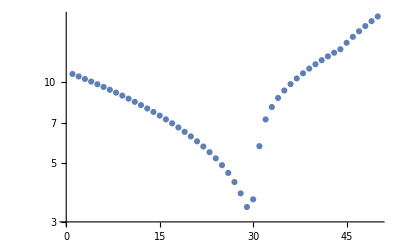

```mathematica
ListLogPlot[EvalsS[[3;;-1;;2]]-EvalsS[[2;;-2;;2]],PlotRange-> Full]
```

```mathematica
Export["Descargas/AvancesT/00_Mathematica/Evals/Eigenvalues.dat",EvalsS]
```

Descargas/AvancesT/00_Mathematica/Eigenvalues.dat

```mathematica
Export["Eigenvectors.dat",VecP]
```

Eigenvectors.dat

```mathematica
Automatización
```

Primero se define γx en el cruce evitado

```mathematica
γxAC1=-(2j-1)/((2j-172)Sqrt[3] );
γxAC2=-(2j-1)/((2j-174)Sqrt[3] );
Clear[k,m]
```

Aquí se guardan los Eigenvalores y Eigenvectores

```mathematica
string1 = "Descargas/AvancesT/00_Mathematica/Evals/";
string2 = "Descargas/AvancesT/00_Mathematica/Evecs/";
string3 = ".dat";
string4 ="Descargas/AvancesT/00_Mathematica/Evals/gmx.dat";
b=10;
```

gmxRange es una lista de valores con los que se realizará la diagonalización a la cual le incluimos los valores de los cruces evitados γxAC1 y γxAC2

```mathematica
gmxRange = Range[-45/10,-39/10,1/80];
AppendTo[gmxRange,γxAC1];
AppendTo[gmxRange,γxAC2];
```

```mathematica
gmx = Sort[gmxRange,Less]
```

{-9/2,-359/80,-179/40,-357/80,-89/20,-71/16,-177/40,-199/(26 √3),-353/80,-22/5,-351/80,-35/8,-349/80,-87/20,-347/80,-173/40,-69/16,-43/10,-343/80,-171/40,-341/80,-17/4,-339/80,-169/40,-337/80,-21/5,-67/16,-167/40,-333/80,-83/20,-331/80,-33/8,-329/80,-199/(28 √3),-41/10,-327/80,-163/40,-65/16,-81/20,-323/80,-161/40,-321/80,-4,-319/80,-159/40,-317/80,-79/20,-63/16,-157/40,-313/80,-39/10}

```mathematica
Monitor[Do[γx=gmx[[a]];
Hmtrx= Table[Table[Hel[j,m,k],{m,-j,j,2}],{k,-j,j,2}];
Evals =Eigenvalues[N[Hmtrx,40]];
VecP = Eigenvectors[N[Hmtrx,40]][[Ordering[Evals]]];
EvalsS= Sort[Evals];
p=StringJoin[string1,ToString[b],string3];
q=StringJoin[string2,ToString[b],string3];
b=b+1;
Export[p,EvalsS];
Export[q,VecP];
,{a,44,51}],a]
```

```mathematica
Export[string4,N[gmx,16]];
```

```mathematica
j=100;
```

```mathematica
N[γxAC1,16]
```

-4.103310841740555

```mathematica
N[γxAC2,16]
```

-4.418950137259059